# Chapter. Coupled chemical reactions

Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[EvaluationNotebook[],
PrintingStartingPageNumber->229,

PageHeaders->{
{Cell[TextData[{CounterBox["Page"]}],FontFamily->"Arial",FontSize->12],Cell[TextData[{"Coupled chemical reactions"}],FontFamily->"Arial",FontSize->12],None},
{None,Cell[TextData[CounterBox["Section",CounterFunction:>(Part[{"Introduction","An EC reaction","An EC reaction with an expanding space grid","A square scheme","Summary","Further reading"},#]&)]],FontFamily->"Arial",FontSize->12], Cell[TextData[{CounterBox["Page"]}],FontFamily->"Arial",FontSize->12]}},

PageFooters->{{None,None,None},{None,None,None}},
PrintingOptions-> {
"PrintingMargins"->{{90,90},{60,90}},
"PaperSize"->{596,794},
"PageSize"->{596,794},
"PageHeaderMargins"->{60,60},
"PageFooterMargins"->{30,30},
"FirstPageFace"->Left,
"FirstPageHeader"->False,
"FirstPageFooter"->False,
"PrintRegistrationMarks"-> False}];
```

```mathematica
Needs["Notation`"];
```

```mathematica
ClearNotations[];
Symbolize[Subscript[k, _]];
```

```mathematica
$TextStyle= {FontFamily-> "Arial",FontSize-> 10, FontWeight->Plain};
$FrameStyle={Black,AbsoluteThickness[.5]};
$ImageSize=288;
```

```mathematica
SetOptions[ListPlot,
Axes->False,
Frame->True,
FrameStyle->$FrameStyle,
GridLines->None,
ImageSize->288,
PlotStyle->{Black,AbsoluteThickness[.5]},
Joined->True];
```

```mathematica
SetOptions[Plot,
Axes->False,
Frame->True,
FrameStyle->$FrameStyle,
GridLines->None,
ImageSize-> 288,
PlotStyle->{Black,AbsoluteThickness[.5]}];
```

```mathematica
(* tick function for labelled axes or frames *)
ticks1[min_,max_,steps_,divs_]:=Chop[Join[Table[{x,x,{0.015,0}},{x,Floor[min],Ceiling[max],steps}],Table[{x,"",{0.0075,0}},{x,Floor[min],Ceiling[max],steps/divs}]]];

(* tick function for non-labelled axes or frames *)
ticks2[min_,max_,steps_,divs_]:=Chop[Join[Table[{x,"",{0.015,0}},{x,Floor[min],Ceiling[max],steps}],Table[{x,"",{0.0075,0}},{x,Floor[min],Ceiling[max],steps/divs}]]];
```

```mathematica
optionA={
PlotStyle->{AbsoluteThickness[0.5]},
FrameLabel->{Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",10,Italic],Style["√πχ",FontFamily->  "Times New Roman",10,Plain],None,None},
FrameTicks->{ticks1[-15,15,5,5],ticks1[-.5,.5,.2,5],ticks2[-15,15,5,5],ticks2[-.5,.5,.2,5]}
};
```

```mathematica
ClearAll[tridiagonalSolveM2];

tridiagonalSolveM2 = Compile[{{x, _Real, 3}, {y, _Real, 3}, {z, _Real, 3}, {b, _Real, 2}},

Module[{len=Length[b],
solution=Table[Table[0.,{Length[b⟦1⟧]}],{Length[b]}],aux ,
β=Table[Table[0.,{Length[x⟦1⟧]},{Length[x⟦1⟧]}],{Length[b]}],iter=0 },

aux=Inverse[y⟦1⟧];

solution⟦1⟧=aux.b⟦1⟧;

Do[β⟦iter⟧=aux.z⟦iter-1⟧;
aux=Inverse[(y⟦iter⟧-x⟦iter-1⟧.β⟦iter⟧)];
solution⟦iter⟧=aux.(b⟦iter⟧-x⟦iter-1⟧.solution⟦iter-1⟧),{iter,2,len}];

Do[solution[[iter]]-=β⟦iter+1⟧.solution⟦iter+1⟧,{iter,len-1,1,-1}];
solution]
];
```

```mathematica
PrependTo[$Path,{
Union[DirectoryName /@ FileNames["*.dat",FileNameJoin[{NotebookDirectory[],"Data","*"}] ,2]],
Union[DirectoryName /@ FileNames["*.nb",FileNameJoin[{NotebookDirectory[],"Extra Notebooks","*"}] ,2]]
}];

$Path=Union[Flatten@$Path];
```

```mathematica
$Line=0;
```

Chapter.Section Introduction

The previous chapters have exclusively considered only simulations involving one or two heterogeneous electrochemical reactions. In reality many electrochemical systems of interest have coupled chemical reactions. The objective of this chapter is to show how to extend the simulation methods described in Chapter 6 to electrochemical systems with coupled chemical reactions. As examples of how to incorporate homogeneous reactions into the simulations methods an electrochemical reaction(s) with a first order homogeneous reaction and a second order homogeneous reaction are simulated.

## Chapter.Section An EC reaction

Consider an electrochemical reaction coupled to a following first order reversible chemical reaction, i.e. an EC reaction.

O+e ⇌R

R ⇌_(k_-1)^(k_(+1)) P

where k_(+1) and k_-1 are homogeneous rate constants. The PDEs for this reaction scheme are:

(∂c_O(x,t))/(∂t)=D_O(∂^2 c_O(x, t))/(∂x^2)

(∂c_R(x,t))/(∂t)=D_R(∂^2 c_R(x, t))/(∂x^2)-k_(+1)c_R(x, t)+k_-1 c_P(x, t)

(∂c_P(x,t))/(∂t)=D_P(∂^2 c_P(x, t))/(∂x^2)+k_(+1)c_R(x, t)-k_-1 c_P(x, t)

Assuming for simplicity that the diffusion coefficients of all species are equal then writing these equations in discrete dimensionless form gives

-D c_(O_(j-1))^(k+1)+(1+2D)c_O_j^(k+1)-D c_(O_(j+1))^(k+1)=c_O_j^k
k_(+1)c_R_j^(k+1)-k_-1 c_P_j^(k+1)-D c_(R_(j-1))^(k+1)+(1+2D)c_R_j^(k+1)-D c_(R_(j+1))^(k+1)=c_R_j^k
-k_(+1)c_R_j^(k+1)+k_-1 c_P_j^(k+1)-D c_(P_(j-1))^(k+1)+(1+2D)c_P_j^(k+1)-D c_(P_(j+1))^(k+1)=c_P_j^k

where the dimensionless homogeneous rate constants are

k_-1=(k_-1)/σ(σΔ t)
k_(+1)=(k_(+1))/σ(σΔ t)

Rearranging eqn (Chapter.EquationNumbered) gives

-D c_(O_(j-1))^(k+1)+(1+2D)c_O_j^(k+1)-D c_(O_(j+1))^(k+1)=c_O_j^k
-D c_(R_(j-1))^(k+1)+(1+2D+k_(+1))c_R_j^(k+1)-k_-1 c_P_j^(k+1)-D c_(R_(j+1))^(k+1)=c_R_j^k
-D c_(P_(j-1))^(k+1)-k_(+1)c_R_j^(k+1)+(1+2D+k_-1)c_P_j^(k+1)-D c_(P_(j+1))^(k+1)=c_P_j^k

Alternatively eqn (Chapter.EquationNumbered) can be written as

X_j·(c_(O_(j-1))^(k+1)
c_(R_(j-1))^(k+1)
c_(P_(j-1))^(k+1))+Y_j·(c_O_j^(k+1)
c_R_j^(k+1)
c_P_j^(k+1))+Z_j·(c_(O_(j+1))^(k+1)
c_(R_(j+1))^(k+1)
c_(P_(j+1))^(k+1))=(c_O_j^k
c_R_j^k
c_P_j^k)

for 2≤ j≤ m-1, where

X_j=Z_j=(-D | 0 | 0
0 | -D | 0
0 | 0 | -D)

and

Y_j=(1+2D | 0 | 0
0 | 1+k_(+1)+2D | -k_-1
0 | -k_(+1) | 1+k_-1+2D)

Thus eqn (Chapter.EquationNumbered) is tridiagonal with each diagonal element being a 3×3 square matrix. When j=2 eqn (Chapter.EquationNumbered) becomes

-D c_O_1^(k+1)+(1+2D)c_O_2^(k+1)-D c_O_3^(k+1)=c_O_2^k
-D c_R_1^(k+1)+(1+2D+k_(+1))c_R_2^(k+1)-k_-1 c_P_2^(k+1)-D c_R_3^(k+1)=c_R_2^k
-D c_P_1^(k+1)-k_(+1)c_R_2^(k+1)+(1+2D+k_-1)c_P_2^(k+1)-D c_P_3^(k+1)=c_P_2^k

To remove c_P_1^(k+1)from eqn (Chapter.EquationNumbered) note that the flux of P at the electrode surface is zero, therefore using the Taylor series approximation (see Appendix 1) we have

c_P_1^(k+1)=4/3 c_P_2^(k+1)-1/3 c_P_3^(k+1)

Substituting eqn (Chapter.EquationNumbered) into (Chapter.EquationNumbered) gives

-D c_O_1^(k+1)+(1+2D)c_O_2^(k+1)-D c_O_3^(k+1)=c_O_2^k
-D c_R_1^(k+1)+(1+2D+k_(+1))c_R_2^(k+1)-k_-1 c_P_2^(k+1)-D  c_R_3^(k+1)=c_R_2^k
-k_(+1)c_R_2^(k+1)+(1+2/3 D+k_-1)c_P_2^(k+1)-2/3 D  c_P_3^(k+1)=c_P_2^k

with now X_2, Z_2 , and Y_2 becoming

X_2=(-D | 0 | 0
0 | -D | 0
0 | 0 | 0)

Z_2=(-D | 0 | 0
0 | -D | 0
0 | 0 | -2/3D)

and

Y_2=(1+2D | 0 | 0
0 | 1+k_(+1)+2D | -k_-1
0 | -k_(+1) | 1+k_-1+2/3 D)

The diagonals X_j, Y_j, and Z_j can be formed using IdentityMatrix.

```mathematica
ClearAll[𝔻,x,y,z,Subscript[k, +1],Subscript[k, -1]];

x=Table[-𝔻*IdentityMatrix[3],{5}];
z=Table[-𝔻*IdentityMatrix[3],{5}];
y=Table[(1+2*𝔻)*IdentityMatrix[3],{5}];
y⟦1⟧+={{0,0,0},{0,Subscript[k, +1],-Subscript[k, -1]},{0,-Subscript[k, +1],Subscript[k, -1]}};
x⟦1,3,3⟧=0;
y⟦1,3,3⟧-=4*𝔻/3;
z⟦1,3,3⟧+=1*𝔻/3;
```

```mathematica
x⟦1⟧//MatrixForm
```

(-𝔻 | 0 | 0
0 | -𝔻 | 0
0 | 0 | 0)

```mathematica
y⟦1⟧//MatrixForm
```

(1+2 𝔻 | 0 | 0
0 | 1+k_(+1)+2 𝔻 | -k_-1
0 | -k_(+1) | 1+k_-1+(2 𝔻)/3)

```mathematica
z⟦1⟧//MatrixForm
```

(-𝔻 | 0 | 0
0 | -𝔻 | 0
0 | 0 | -(2 𝔻)/3)

The dimensionless form of the Butler-Volmer equation (§.6.5) allows the determination of c_O_1^(k+1)and c_R_1^(k+1).

3 c_O_1^(k+1)-4 c_O_2^(k+1)+c_O_3^(k+1)=2k_s^*(c_R_1^(k+1)ξ^(1-α)-c_O_1^(k+1)ξ^-α)

with

k_s^*=(k_s( t_n/(D(n-1))))^(1/2)

To include the boundary condition at the electrode surface we note that the sum of the fluxes of O and R at the electrode surface are zero.

3 c_O_1^(k+1)-4 c_O_2^(k+1)+c_O_3^(k+1)+3 c_R_1^(k+1)-4 c_R_2^(k+1)+c_R_3^(k+1)=0

Combining eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered) and rearranging gives

(3+2 k_s^*ξ^-α)c_O_1^(k+1)-2 k_s^*ξ^(1-α)c_R_1^(k+1)-4 c_O_2^(k+1)+c_O_3^(k+1)=0
3 c_O_1^(k+1)+3 c_R_1^(k+1)-4 c_O_2^(k+1)-4 c_R_2^(k+1)+c_O_3^(k+1)+c_R_3^(k+1)=0

Equation (Chapter.EquationNumbered) can be re-written in matrix form as

(3+2 k_s^*ξ^-α | -2 k_s^*ξ^(1-α)
3 | 3)(c_O_1^(k+1)
c_R_1^(k+1))-(4 | 0
4 | 4)(c_O_2^(k+1)
c_R_2^(k+1))+(1 | 0
1 | 1)(c_O_3^(k+1)
c_R_3^(k+1))=0

Solving for c_O_1^(k+1)and c_R_1^(k+1)gives

(c_O_1^(k+1)
c_R_1^(k+1))=4B_1^-1·B_2·(c_O_2^(k+1)
c_R_2^(k+1))-B_1^-1·B_2·(c_O_3^(k+1)
c_R_3^(k+1))

where B_1^-1·B_2  is the dot product of the inverse of B_1, where B_1 is

B_1=(3+2 k_s^*ξ^-α | -2 k_s^*ξ^(1-α)
3 | 3)

and B_2

B_2=(1 | 0
1 | 1)

These values of c_O_1^(k+1) and c_R_1^(k+1) can be included by taking the first two rows from eqn (Chapter.EquationNumbered) which for   j=2 are

X_2^*·(c_O_1^(k+1)
c_R_1^(k+1))+Y_2^*·(c_O_2^(k+1)
c_R_2^(k+1))+Z_2^*·(c_O_3^(k+1)
c_R_3^(k+1))=(c_O_2^k
c_R_2^k)

where X_2^*, Y_2^* and Z_2^* are the 2 × 2 blocks in the upper left hand corner of the matrices X_2, Y_2 and Z_2 respectively. For example X_2^* is shown below:

X_2=((-D | 0
0 | -D) | 0
0
0 | 0 | -D)=(X_2^* | 0
0
0 | 0 | -D)

Substituting eqn (Chapter.EquationNumbered) into eqn (Chapter.EquationNumbered) gives

(Y_2^*+4X_2^*·B_1^-1·B_2)·(c_O_2^(k+1)
c_R_2^(k+1))+(Z_2^*-X_2^*·B_1^-1·B_2)·(c_O_3^(k+1)
c_R_3^(k+1))=(c_O_2^k
c_R_2^k)

Therefore the revised diagonal elements Y_2, and Z_2 become

Y_2=((Y_2^*+4X_2^*·B_1^-1·B_2) | 0
-k_-1
0 |           -k_(+1) | 1+k_-1+2/3 D)

and

Z_2=((Z_2^*-X_2^*·B_1^-1·B_2) | 0
0
0 |            0 | -2/3D)

Y_2 and Z_2 need to be updated at each time increment but this can be done in the same way as one dimensional elements Y_2 and Z_2 were updated when simulating voltammograms without coupled reactions (§6.5). Firstly the value of B_1^-1·B_2 is calculated at a given time increment.

```mathematica
ClearAll[b1,Subscript[k, +1],Subscript[k, -1]];
b1=Inverse[{{3+2*Subscript[k, +1],-2*Subscript[k, -1]},{3,3}}]//Simplify;
b1//MatrixForm
```

(1/(3+2 k_-1+2 k_(+1)) | (2 k_-1)/(9+6 k_-1+6 k_(+1))
1/(-3-2 k_-1-2 k_(+1)) | (3+2 k_(+1))/(9+6 k_-1+6 k_(+1)))

X_2^* is constant throughout the simulation and can be declared as a separate constant. Also the initial values of Y_2 and Z_2, y⟦1⟧ and z⟦1⟧, prior to the start of the simulation are stored as separate constants.

```mathematica
ClearAll[y1,z1,x1];

y1=y⟦1⟧;
z1=z⟦1⟧;
x1=Take[x⟦1⟧,{1,2},{1,2}];
x1//MatrixForm
```

(-𝔻 | 0
0 | -𝔻)

Y_2 and Z_2 can then be updated.

```mathematica
ClearAll[b2];

b2={{1,0},{1,1}};
y⟦1,{1,2},{1,2}⟧+=4*(x1.b1.b2);
z⟦1,{1,2},{1,2}⟧-=(x1.b1.b2);
```

The matrices can be checked to ensure that they have been formed correctly:

```mathematica
y⟦1⟧//MatrixForm
```

(1+2 𝔻+4 (-𝔻/(3+2 k_-1+2 k_(+1))-(2 k_-1 𝔻)/(9+6 k_-1+6 k_(+1))) | -(8 k_-1 𝔻)/(9+6 k_-1+6 k_(+1)) | 0
4 (-𝔻/(-3-2 k_-1-2 k_(+1))-((3+2 k_(+1)) 𝔻)/(9+6 k_-1+6 k_(+1))) | 1+k_(+1)+2 𝔻-(4 (3+2 k_(+1)) 𝔻)/(9+6 k_-1+6 k_(+1)) | -k_-1
0 | -k_(+1) | 1+k_-1+(2 𝔻)/3)

Note that the output from this execution spreads across two pages.

```mathematica
z⟦1⟧//MatrixForm
```

(-𝔻+𝔻/(3+2 k_-1+2 k_(+1))+(2 k_-1 𝔻)/(9+6 k_-1+6 k_(+1)) | (2 k_-1 𝔻)/(9+6 k_-1+6 k_(+1)) | 0
𝔻/(-3-2 k_-1-2 k_(+1))+((3+2 k_(+1)) 𝔻)/(9+6 k_-1+6 k_(+1)) | -𝔻+((3+2 k_(+1)) 𝔻)/(9+6 k_-1+6 k_(+1)) | 0
0 | 0 | -(2 𝔻)/3)

The diagonals X_j, Y_j, and Z_j are now complete. The vector b can be formed in the same way as for voltammetry in the absence of coupled reactions. The solution at a given time step can be obtained using the tridiagonal matrix solver tridiagonalSolveM2 (§4.3).

temp=tridiagonalSolveM2[x,y,z,b];

After obtaining the solution for 2≤ j≤ m-1 the boundary values of O, R and P are added. At the electrode surface these values are calculated from eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered). The vectors (c_O_2^(k+1)
c_R_2^(k+1)) and (c_O_3^(k+1)
c_R_3^(k+1)) used in eqn (Chapter.EquationNumbered) are obtained from the first and second elements of the tridiagonal solution, i.e. temp⟦1,{1,2}⟧ and temp⟦2,{1,2}⟧, for example:

```mathematica
ClearAll[temp,c];

temp={{Subscript[c, O2]^(k+1),Subscript[c, R2]^(k+1),Subscript[c, P2]^(k+1)},{Subscript[c, O3]^(k+1),Subscript[c, R3]^(k+1),Subscript[c, P3]^(k+1)},{Subscript[c, O4]^(k+1),Subscript[c, R4]^(k+1),Subscript[c, P4]^(k+1)},other terms,{Subscript[c, Om-1]^(k+1),Subscript[c, Rm-1]^(k+1),Subscript[c, Pm-1]^(k+1)}};

temp⟦1,{1,2}⟧
temp⟦2,{1,2}⟧
```

{c_O2^(1+k),c_R2^(1+k)}

{c_O3^(1+k),c_R3^(1+k)}

c_P_2^(k+1) and c_P_3^(k+1) are

```mathematica
temp⟦1,3⟧
temp⟦2,3⟧
```

c_P2^(1+k)

c_P3^(1+k)

The list of concentrations at the (k+1)th time increment is therefore:

Join[Flatten[b1.(4*temp⟦1,{1,2}⟧-temp⟦2,{1,2}⟧),{(4.*temp⟦1,3⟧/3.)-temp⟦2,3⟧/3.}],temp,{{1.,0.,0.}}];

Finally at each time step at the end of the calculation Y_2 and Z_2 are required to revert to their initial values, eg. y1 and z1.

```mathematica
y⟦1⟧=y1;
z⟦1⟧=z1;
```

A full implementation is given in the notebook coupledECRxn.nb.

## Chapter.Section An EC reaction with an expanding space grid

To computation time can be reduced with an expanding grid. With reference to §4.3.3 eqn (Chapter.EquationNumbered) can be re-written as

-a D_j c_(O_(j-1))^(k+1)+(1+(1+a)D_j)c_O_j^(k+1)-D_j c_(O_(j+1))^(k+1)=c_O_j^k
k_(+1)c_R_j^(k+1)-k_-1 c_P_j^(k+1)-a D_j c_(R_(j-1))^(k+1)+(1+(1+a)D_j)c_R_j^(k+1)-D_j c_(R_(j+1))^(k+1)=c_R_j^k
-k_(+1)c_R_j^(k+1)+k_-1 c_P_j^(k+1)-a D_j c_(P_(j-1))^(k+1)+(1+(1+a)D_j)c_P_j^(k+1)-D_j c_(P_(j+1))^(k+1)=c_P_j^k

where

D_j=D^*a^(3-2j)

and

D^*=(2DΔt)/((1+a)(Δx)^2)

Equations (Chapter.EquationNumbered), and (Chapter.EquationNumbered) become

X_j=(-a D_j | 0 | 0
0 | -a D_j | 0
0 | 0 | -a D_j)

Z_j=(-D_j | 0 | 0
0 | -D_j | 0
0 | 0 | -D_j)

and

Y_j=(1+(1+a)D_j | 0 | 0
0 | 1+k_(+1)+(1+a)D_j | -k_-1
0 | -k_(+1) | 1+k_-1+(1+a)D_j)

When j=2 eqn (Chapter.EquationNumbered) becomes

-a D_2 c_O_1^(k+1)+(1+(1+a)D_2)c_O_2^(k+1)-D_2 c_O_3^(k+1)=c_O_2^k
-a D_2 c_R_1^(k+1)+(1+(1+a)D_2+k_(+1))c_R_2^(k+1)-k_-1 c_P_2^(k+1)-D_2 c_R_3^(k+1)=c_R_2^k
-a D_2 c_P_1^(k+1)-k_(+1)c_R_2^(k+1)+(1+(1+a)D_2+k_-1)c_P_2^(k+1)-D_2 c_P_3^(k+1)=c_P_2^k

Substituting eqn (Chapter.EquationNumbered) into (Chapter.EquationNumbered) to remove c_P_1^(k+1) gives

X_2=(-a D_2 | 0 | 0
0 | -a D_2 | 0
0 | 0 | 0)

Z_2=(-D_2 | 0 | 0
0 | -D_2 | 0
0 | 0 | -D_2+1/(a(2+a))D_2)

and

Y_2=(1+(1+a)D_2 | 0 | 0
0 | 1+k_(+1)+(1+a)D_2 | -k_-1
0 | -k_(+1) | 1+k_-1+(1+a)D_2-(1+a)^2/(a(2+a))D_2)

```mathematica
ClearAll[makeDiagonals];

makeDiagonals[m_Integer,d_][a_][kf_,kb_]:=Module[{x,y,z},
x=Table[-a*d*a^(3-2*j)*IdentityMatrix[3],{j,2,m-1}];
z=Table[-d*a^(3-2*j)*IdentityMatrix[3],{j,2,m-2}];
y=Table[(1+(1+a)*d*a^(3-2*j))*IdentityMatrix[3]+{{0,0,0},{0,kf,-kb},{0,-kf,kb}},{j,2,m-1}];
x⟦1,3,3⟧=0;
y⟦1,3,3⟧-=(1+a)^2/(a*(2+a))*d*a^(3-4);
z⟦1,3,3⟧+=1/(a*(2+a))*d*a^(3-4);
{x,y,z}]
```

The dimensionless form of the Butler-Volmer equation, written in terms of the three point approximation for the flux, allows the determination of c_O_1^(k+1)and c_R_1^(k+1).

a(2+a)c_O_1^(k+1)-(1+a)^2 c_O_2^(k+1)+c_O_3^(k+1)=a(1+a)k_s^*(c_R_1^(k+1)ξ^(1-α)-c_O_1^(k+1)ξ^-α)

with

k_s^*=a(1+a)(k_s((2 t_n)/(D^*(1+a)(n-1))))^(1/2)

The fluxes of O and R at the electrode surface are zero:

a(2+a)c_O_1^(k+1)-(1+a)^2 c_O_2^(k+1)+c_O_3^(k+1)+a(2+a)c_R_1^(k+1)-(1+a)^2 c_R_2^(k+1)+c_R_3^(k+1)=0

Combining eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered) and rearranging gives

(a(2+a)+k_s^*ξ^-α)c_O_1^(k+1)-k_s^*ξ^(1-α)c_R_1^(k+1)-(1+a)^2 c_O_2^(k+1)+c_O_3^(k+1)=0
a(2+a)c_O_1^(k+1)+a(2+a)c_R_1^(k+1)-(1+a)^2 c_O_2^(k+1)-(1+a)^2 c_R_2^(k+1)+c_O_3^(k+1)+c_R_3^(k+1)=0

Equation (Chapter.EquationNumbered) can be re-written in matrix form as

(a(2+a)+k_s^*ξ^-α | -k_s^*ξ^(1-α)
a(2+a) | a(2+a))(c_O_1^(k+1)
c_R_1^(k+1))-((1+a)^2 | 0
(1+a)^2 | (1+a)^2)(c_O_2^(k+1)
c_R_2^(k+1))+(1 | 0
1 | 1)(c_O_3^(k+1)
c_R_3^(k+1))=0

Solving for c_O_1^(k+1) and c_R_1^(k+1) gives

(c_O_1^(k+1)
c_R_1^(k+1))=B_1^-1·B_3·(c_O_2^(k+1)
c_R_2^(k+1))-B_1^-1·B_2·(c_O_3^(k+1)
c_R_3^(k+1))

where B_1^-1 is the inverse of B_1

B_1=(a(2+a)+k_s^*ξ^-α | -k_s^*ξ^(1-α)
a(2+a) | a(2+a))

B_2 is given by eqn (Chapter.EquationNumbered) and B_3 is

B_3=((1+a)^2 | 0
(1+a)^2 | (1+a)^2)

After making these changes the function used to solve the concentration profile at each time step is therefore:

```mathematica
ClearAll[solveEC];

solveEC[list_List,k_Integer]:=Module[{ξ,b,b1,tmp},

ξ=If[k>(n+1)/2,Exp[upperLimit-range+(τ*(k-1))],Exp[upperLimit-(τ*(k-1))]];
y⟦1⟧=y1;
z⟦1⟧=z1;
b=list[[2;;-2]];
b⟦-1⟧+={d*a^(5-2*m),0.,0.};
b1=Inverse[{{a*(2+a)+a*(1+a)*ksStar*ξ^-α,-a*(1+a)*ksStar*ξ^(1.-α)},{a*(2+a),a*(2+a)}}];
y⟦1,{1,2},{1,2}⟧+=xstar.b1.b3;
z⟦1,{1,2},{1,2}⟧-=xstar.b1.b2;
tmp=tridiagMatSolver[x,y,z,b];
Join[{Join[b1.b3.tmp⟦1,{1,2}⟧-b1.b2.tmp⟦2,{1,2}⟧,{((1+a)^2*tmp⟦1,3⟧-tmp⟦2,3⟧)/(a*(2+a))}]},tmp,{{1.,0.,0.}}]
]
```

The full implementation is given in the notebook coupledECRxnExp.nb.

Code for Fig Chapter.FigureCaption

```mathematica
ClearAll[upperLimit,𝕥,n,τ,𝔻,a];
upperLimit=10.(*initial potential versus the formal potential*);
𝕥 =40.;(*the region or range of the sweep*)
n=205;
τ=𝕥/(n-1);(*calculation of the incremental time/potential step*)
a=1.1;(*grid expansion factor*)
```

```mathematica
ClearAll[c1,𝔻,cv1,cv2,plot1];

c1=<<ec1.dat;
𝔻=2.;
cv1=Map[(((a*(2+a)*#⟦1⟧-((1+a)^2*#⟦2⟧)+#⟦3⟧)/(a*(1+a)))*√((𝔻*(1+a)*(n-1))/(2*𝕥)))&,c1⟦All,All,1⟧];

cv2=Table[{If[j>(n+1)/2,upperLimit-𝕥+τ*(j-1),upperLimit-(𝕥*(j-1)/(n-1))],cv1⟦j⟧},{j,1,Length[cv1]}];

plot1=ListPlot[cv2,PlotStyle->Black,optionA];
```

```mathematica
ClearAll[c2,𝔻,cv1,cv2,plot2];

c2=<<ec2.dat;
𝔻=2.;
cv1=Map[(((a*(2+a)*#⟦1⟧-((1+a)^2*#⟦2⟧)+#⟦3⟧)/(a*(1+a)))*√((𝔻*(1+a)*(n-1))/(2*𝕥)))&,c2⟦All,All,1⟧];

cv2=Table[{If[j>(n+1)/2,upperLimit-𝕥+τ*(j-1),upperLimit-(𝕥*(j-1)/(n-1))],cv1⟦j⟧},{j,1,Length[cv1]}];

plot2=ListPlot[cv2,PlotStyle-> {Black,Dashing[{0.02,0.005}]},optionA];
```

```mathematica
ClearAll[c3,𝔻,cv1,cv2,plot3];

c3=<<ec3.dat;
𝔻=39.2157;

cv1=Map[(((a*(2+a)*#⟦1⟧-((1+a)^2*#⟦2⟧)+#⟦3⟧)/(a*(1+a)))*√((𝔻*(1+a)*(n-1))/(2*𝕥)))&,c3⟦All,All,1⟧];

cv2=Table[{If[j>(n+1)/2,upperLimit-𝕥+τ*(j-1),upperLimit-(𝕥*(j-1)/(n-1))],cv1⟦j⟧},{j,1,Length[cv1]}];

plot3=ListPlot[cv2,PlotStyle-> {Black,Dashing[{0.01,0.005}]},optionA];
```

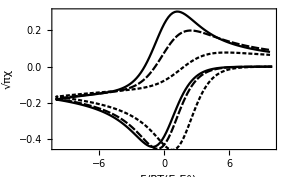

```mathematica
Show[plot1,plot2,plot3]
```

Fig. Chapter.FigureCaption  Simulated cyclic voltammogram of an EC mechanism. Simulation parameters: n=205, k_s=10, τ=40/(n-1), k_-1=τ, and k_(+1)=0.1τ, 2τ, and 40τ.

## Chapter.Section A square scheme

Consider a square scheme.

O+e | ⇌ | R
k_-1 ⥮ k_(+1) |   | k_-2 ⥮ k_(+2)
A+e | ⇌ | B

where k_(+1), k_(+2), k_-1 and k_-2 are homogeneous rate constants. The cross reaction is

O+B⇌_k_cb^k_cf A+R

with k_cf, and k_cb homogeneous rate constants for the cross reaction. The following equilibrium constant can be defined:

K_OA=(k_(+1))/(k_-1)

K_RB=(k_(+2))/(k_-2)

K_cr=k_cf/k_cb=K_OA/K_RB=exp((n F)/(R T)(E_OR^o-E_AB^o))

The PDEs for this reaction scheme are:

(∂c_O(x,t))/(∂t)=D_O(∂^2 c_O(x, t))/(∂x^2)-k_(+1)c_O(x, t)+k_-1 c_A(x, t)-k_cf c_O(x, t)c_B(x, t)+k_cb c_A(x, t)c_R(x, t)

(∂c_R(x,t))/(∂t)=D_R(∂^2 c_R(x, t))/(∂x^2)-k_(+2)c_R(x, t)+k_-2 c_B(x, t)+k_cf c_O(x, t)c_B(x, t)-k_cb c_A(x, t)c_R(x, t)

(∂c_A(x,t))/(∂t)=D_A(∂^2 c_A(x, t))/(∂x^2)+k_(+1)c_O(x, t)-k_-1 c_A(x, t)+k_cf c_O(x, t)c_B(x, t)-k_cb c_A(x, t)c_R(x, t)

(∂c_B(x,t))/(∂t)=D_B(∂^2 c_B(x, t))/(∂x^2)+k_(+2)c_R(x, t)-k_-2 c_B(x, t)-k_cf c_O(x, t)c_B(x, t)+k_cb c_A(x, t)c_R(x, t)

Assuming for simplicity that the diffusion coefficients are equal, then writing these equations in discrete dimensionless form gives

k_cf c_O_j^(k+1)c_B_j^(k+1)-k_cb c_A_j^(k+1)c_R_j^(k+1)+k_(+1)c_O_j^(k+1)-k_-1 c_A_j^(k+1)-D c_(O_(j-1))^(k+1)+(1+2D)c_O_j^(k+1)-D c_(O_(j+1))^(k+1)=c_O_j^k
-k_cf c_O_j^(k+1)c_B_j^(k+1)+k_cb c_A_j^(k+1)c_R_j^(k+1)+k_(+2)c_R_j^(k+1)-k_-2 c_B_j^(k+1)-D c_(R_(j-1))^(k+1)+(1+2D)c_R_j^(k+1)-D c_(R_(j+1))^(k+1)=c_R_j^k
-k_cf c_O_j^(k+1)c_B_j^(k+1)+k_cb c_A_j^(k+1)c_R_j^(k+1)-k_(+1)c_O_j^(k+1)+k_-1 c_A_j^(k+1)-D c_(A_(j-1))^(k+1)+(1+2D)c_A_j^(k+1)-D c_(A_(j+1))^(k+1)=c_A_j^k
k_cf c_O_j^(k+1)c_B_j^(k+1)-k_cb c_A_j^(k+1)c_R_j^(k+1)-k_(+2)c_R_j^(k+1)+k_-2 c_B_j^(k+1)-D c_(B_(j-1))^(k+1)+(1+2D)c_B_j^(k+1)-D c_(B_(j+1))^(k+1)=c_B_j^k

where the dimensionless homogeneous rate constants are

k_(+1)=k_(+1)Δ t
k_(+2)=k_(+2)Δ t
k_-1=k_-1 Δ t
k_-2=k_-2 Δ t
k_cf=k_cf Δ t
k_cb=k_cb Δ t

Rearranging eqn (Chapter.EquationNumbered) gives

-D  c_(O_(j-1))^(k+1)+(1+2D+k_(+1)+k_cf c_B_j^(k+1))c_O_j^(k+1)-(k_cb c_R_j^(k+1)+k_-1)c_A_j^(k+1)-D c_(O_(j+1))^(k+1)=c_O_j^k
-D  c_(R_(j-1))^(k+1)+(1+2D+k_(+2)+k_cb c_A_j^(k+1))c_R_j^(k+1)-(k_cf c_O_j^(k+1)+k_-2)c_B_j^(k+1)-D c_(R_(j+1))^(k+1)=c_R_j^k
-D  c_(A_(j-1))^(k+1)+(1+2D+k_-1+k_cb c_R_j^(k+1))c_A_j^(k+1)-(k_cf c_B_j^(k+1)+k_(+1))c_O_j^(k+1)-D c_(A_(j+1))^(k+1)=c_A_j^k
-D  c_(B_(j-1))^(k+1)+(1+2D+k_-2+k_cf c_O_j^(k+1))c_B_j^(k+1)-(k_cb c_A_j^(k+1)+k_(+2))c_R_j^(k+1)-D c_(B_(j+1))^(k+1)=c_B_j^k

Alternatively eqn (Chapter.EquationNumbered) can be written as

X_j·(c_(O_(j-1))^(k+1)
c_(R_(j-1))^(k+1)
c_(A_(j-1))^(k+1)
c_(B_(j-1))^(k+1))+Y_j·(c_O_j^(k+1)
c_R_j^(k+1)
c_A_j^(k+1)
c_B_j^(k+1))+Z_j·(c_(O_(j+1))^(k+1)
c_(R_(j+1))^(k+1)
c_(A_(j+1))^(k+1)
c_(B_(j+1))^(k+1))=(c_O_j^k
c_R_j^k
c_A_j^k
c_B_j^k)

for 2≤ j≤ m-1, where

X_j=Z_j=(-D | 0 | 0 | 0
0 | -D | 0 | 0
0 | 0 | -D | 0
0 | 0 | 0 | -D)

and

Y_j=

(1+2D+k_(+1)+k_cf c_B_j^(k+1) | 0 | -k_cb c_R_j^(k+1)-k_-1 | 0
0 | 1+2D+k_-2+k_cb c_A_j^(k+1) | 0 | -k_cf c_O_j^(k+1)-k_-2
-k_cf c_B_j^(k+1)-k_(+1) | 0 | 1+2D+k_-1+k_cb c_R_j^(k+1) | 0
0 | -k_cb c_A_j^(k+1)-k_(+2) | 0 | 1+2D+k_-2+k_cf c_O_j^(k+1))

The matrix Y_j can be constructed as a sum of a constant matrix and a matrix that varies at each time step. For clarity the solution for a fixed width grid is shown.

```mathematica
ClearAll[yConst,m,a,𝔻,Subscript[k, -1],Subscript[k, -2],Subscript[k, +1],Subscript[k, +2]];

m=10;
yConst=Table[1+2*𝔻*IdentityMatrix[4]+{{Subscript[k, +1],0,-Subscript[k, -1],0},{0,Subscript[k, +2],0,-Subscript[k, -2]},{-Subscript[k, +1],0,+Subscript[k, -1],0},{0,-Subscript[k, +2],0,Subscript[k, -2]}},{m-2}];
```

```mathematica
ClearAll[yVar];

yVar:={{Subscript[k, cf]*#⟦4⟧,0,-Subscript[k, cb]*#⟦2⟧,0},{0,Subscript[k, cb]*#⟦3⟧,0,-Subscript[k, cf]*#⟦1⟧},{-Subscript[k, cf]*#⟦4⟧,0,Subscript[k, cb]*#⟦2⟧,0},{0,-Subscript[k, cb]*#⟦3⟧,0,Subscript[k, cf]*#⟦1⟧}}&;
```

```mathematica
Clear[cO,cR,cA,cB];
concsList=Table[{cO[j,k+1],cR[j,k+1],cA[j,k+1],cB[j,k+1]},{j,2,m-1}];

y=yConst+yVar/@concsList;
```

```mathematica
y⟦1⟧//MatrixForm
```

(1+k_(+1)+2 𝔻+k_cf cB[2,1+k] | 1 | 1-k_-1-k_cb cR[2,1+k] | 1
1 | 1+k_(+2)+2 𝔻+k_cb cA[2,1+k] | 1 | 1-k_-2-k_cf cO[2,1+k]
1-k_(+1)-k_cf cB[2,1+k] | 1 | 1+k_-1+2 𝔻+k_cb cR[2,1+k] | 1
1 | 1-k_(+2)-k_cb cA[2,1+k] | 1 | 1+k_-2+2 𝔻+k_cf cO[2,1+k])

Note that the output from this execution spreads across two pages.

When   j=2

-D c_O_1^(k+1)+(1+2D+k_(+1)+k_cf c_B_2^(k+1))c_O_2^(k+1)-(k_cb c_R_2^(k+1)+k_-1)c_A_2^(k+1)-D c_O_3^(k+1)=c_O_2^k
-D c_R_1^(k+1)+(1+2D+k_(+2)+k_cb c_A_2^(k+1))c_R_2^(k+1)-(k_cf c_O_2^(k+1)+k_-2)c_B_2^(k+1)-D c_R_3^(k+1)=c_R_2^k
-D c_A_1^(k+1)+(1+2D+k_-1+k_cb c_R_2^(k+1))c_A_2^(k+1)-(k_cf c_B_2^(k+1)+k_(+1))c_O_2^(k+1)-D c_A_3^(k+1)=c_A_2^k
-D c_B_1^(k+1)+(1+2D+k_-2+k_cf c_O_2^(k+1))c_B_2^(k+1)-(k_cb c_A_2^(k+1)+k_(+2))c_R_2^(k+1)-D c_B_3^(k+1)=c_B_2^k

The boundary conditions at the electrode surface are determined from the dimensionless Butler-Volmer equation. For clarity the solution for a fixed width grid is shown.

(3 c_O_1^k-4 c_O_2^k+c_O_3^k)=2k_s1^*(c_R_1^k ξ_1^(1-α)-c_O_1^k ξ_1^-α)

3 c_O_1^k-4 c_O_2^k+c_O_3^k+3 c_R_1^k-4 c_R_2^k+c_R_3^k=0

(3 c_A_1^k-4 c_A_2^k+c_A_3^k)=2k_s2^*(c_B_1^k ξ_2^(1-α)-c_A_1^k ξ_2^-α)

3 c_A_1^k-4 c_A_2^k+c_A_3^k+3 c_B_1^k-4 c_B_2^k+c_B_3^k=0

Rearranging these four equations gives:

(3+2 k_s1^*ξ_1^-α)c_O_1^k-2 k_s1^*ξ_1^(1-α)c_R_1^k-4 c_O_2^k+c_O_3^k=0
3 c_O_1^k+3 c_R_1^k-4 c_O_2^k-4 c_R_2^k+c_O_3^k+c_R_3^k=0
(3+2 k_s2^*ξ_2^-α)c_A_1^k-2 k_s2^*ξ_2^(1-α)c_B_1^k-4 c_A_2^k+c_A_3^k=0
3 c_A_1^k+3 c_B_1^k-4 c_A_2^k-4 c_B_2^k+c_A_3^k+c_B_3^k=0

Equations (Chapter.EquationNumbered) to (Chapter.EquationNumbered) can be re-written in matrix form as

(c_O_1^(k+1)
c_R_1^(k+1)
c_A_1^(k+1)
c_B_1^(k+1))=4B_1^-1·B_2(c_O_2^(k+1)
c_R_2^(k+1)
c_A_2^(k+1)
c_B_2^(k+1))-B_1^-1·B_2(c_O_3^(k+1)
c_R_3^(k+1)
c_A_3^(k+1)
c_B_3^(k+1))

where B_1^-1 is the inverse of B_1.

B_1=(3+2 k_s1^*ξ_1^-α | -2 k_s1^*ξ_1^(1-α) | 0 | 0
0 | 0 | 3+2 k_s2^*ξ_2^-α | -2 k_s2^*ξ_2^(1-α)
3 | 3 | 0 | 0
0 | 0 | 3 | 3)

and

B_2=(1 | 0 | 0 | 0
0 | 0 | 1 | 0
1 | 1 | 0 | 0
0 | 0 | 1 | 1)

When   j=2 eqn (Chapter.EquationNumbered) can becomes

X_2·(c_O_1^(k+1)
c_R_1^(k+1)
c_A_1^(k+1)
c_B_1^(k+1))+Y_2·(c_O_2^(k+1)
c_R_2^(k+1)
c_A_2^(k+1)
c_B_2^(k+1))+Z_2·(c_O_3^(k+1)
c_R_3^(k+1)
c_A_3^(k+1)
c_B_3^(k+1))=(c_O_2^k
c_R_2^k
c_A_2^k
c_B_2^k)

Substituting eqn (Chapter.EquationNumbered) into eqn (Chapter.EquationNumbered) gives

(Y_2+4X_2·B_1^-1·B_2)·(c_O_2^(k+1)
c_R_2^(k+1)
c_A_2^(k+1)
c_B_2^(k+1))+(Z_2-X_2·B_1^-1·B_3)·(c_O_3^(k+1)
c_R_3^(k+1)
c_A_3^(k+1)
c_B_3^(k+1))=(c_O_2^k
c_R_2^k
c_A_2^k
c_B_2^k)

From eqn (Chapter.EquationNumbered) we can see that eqn (Chapter.EquationNumbered) is non-linear because eqn (Chapter.EquationNumbered) contains concentration terms at the k+1 time increment, however if the cross reaction were ignored the problem would become linear and can be solved in the same way as the EC reaction in the previous section. Fig 13.FigureCaption shows some examples of square schemes simulated with the cross reaction rate constants k_cf=k_cb=0.

A full implementation is given in the notebook SquareRxnExp1.nb.

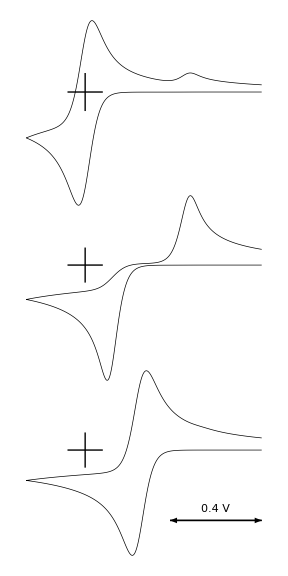

```mathematica
<<fig132.dat
```

Fig. Chapter.FigureCaption  Simulated cyclic voltammogram of a square scheme with reversible electrochemical steps and without the cross reaction. Simulation parameters: Initial dimensionless potential E=30, E_OR=0, E_AB=19.47, K_RB=10^4, k_-1=10^2, and (top to bottom) k_(+2)=10^-2, 10^4, 10^10. Expanding grid used with a=1.1, n=1027 and (top to bottom) m=52, 76, 149.

When the cross reaction is taken into account eqn (Chapter.EquationNumbered) becomes non-linear, however it can be convenient to use the following linear approximation obtained by re-writing c_j^(k+1) as c_j^(k+1)=c_j^k+δc_j:

c_B_j^(k+1)c_O_j^(k+1)=(c_B_j^k+δc_B_j)(c_O_j^k+δc_O_j)
=c_B_j^k c_O_j^k+c_B_j^k δc_O_j+δc_B_j c_O_j^k+δc_B_j δc_O_j
=c_B_j^k(c_O_j^k+δc_O_j)+c_O_j^k(c_B_j^k+δc_B_j)+δc_B_j δc_O_j-c_B_j^k c_O_j^k

Assuming that the term δc_B_j δc_O_j is negligible this approximation reduces to

c_B_j^(k+1)c_O_j^(k+1)≈c_B_j^k c_O_j^(k+1)+c_O_j^k c_B_j^(k+1)-c_B_j^k c_O_j^k

Using this approximation eqn (Chapter.EquationNumbered) becomes

-D c_(O_(j-1))^(k+1)+(1+2D+k_(+1)+k_cf c_B_j^k)c_O_j^(k+1)-k_cb c_A_j^k c_R_j^(k+1)-(k_cb c_R_j^k+k_-1)c_A_j^(k+1)+k_cf c_O_j^k c_B_j^(k+1)-D c_(O_(j+1))^(k+1)=c_O_j^k+k_cf c_B_j^k c_O_j^k-k_cb c_A_j^k c_R_j^k
-D c_(O_(j-1))^(k+1)+(1+2D+k_(+1)+k_cf c_B_j^k)c_O_j^(k+1)-k_cb c_A_j^k c_R_j^(k+1)-(k_cb c_R_j^k+k_-1)c_A_j^(k+1)+k_cf c_O_j^k c_B_j^(k+1)-D c_(O_(j+1))^(k+1)=c_O_j^k+k_cf c_B_j^k c_O_j^k-k_cb c_A_j^k c_R_j^k-D c_(R_(j-1))^(k+1)-k_cf c_B_j^k c_O_j^(k+1)+(1+2D+k_(+2)+k_cb c_A_j^k)c_R_j^(k+1)+k_cb c_R_j^k c_A_j^(k+1)-(k_cf c_O_j^k+k_-2)c_B_j^(k+1)-D c_(R_(j+1))^(k+1)=c_R_j^k+k_cb c_A_j^k c_R_j^k-k_cf c_B_j^k c_O_j^k-D c_(A_(j-1))^(k+1)-(k_cf c_B_j^k+k_(+1))c_O_j^(k+1)+k_cb c_A_j^k c_R_j^(k+1)+(1+2D+k_-1+k_cb c_R_j^k)c_A_j^(k+1)-k_cf c_O_j^k c_B_j^(k+1)-D c_(A_(j+1))^(k+1)=c_A_j^k+k_cb c_R_j^k c_A_j^k-k_cf c_B_j^k c_O_j^k
-D c_(B_(j-1))^(k+1)+k_cf c_B_j^k c_O_j^(k+1)-(k_cb c_A_j^k+k_(+2))c_R_j^(k+1)-k_cb c_R_j^k c_A_j^(k+1)+(1+2D+k_-2+k_cf c_O_j^k)c_B_j^(k+1)-D c_(B_(j+1))^(k+1)=c_B_j^k+k_cf c_B_j^k c_O_j^k-k_cb c_A_j^k c_R_j^k

X_j·(c_(O_(j-1))^(k+1)
c_(R_(j-1))^(k+1)
c_(A_(j-1))^(k+1)
c_(B_(j-1))^(k+1))+Y_j·(c_O_j^(k+1)
c_R_j^(k+1)
c_A_j^(k+1)
c_B_j^(k+1))+Z_j·(c_(O_(j+1))^(k+1)
c_(R_(j+1))^(k+1)
c_(A_(j+1))^(k+1)
c_(B_(j+1))^(k+1))=(c_O_j^k+k_cf c_B_j^k c_O_j^k-k_cb c_A_j^k c_R_j^k
c_R_j^k+k_cb c_A_j^k c_R_j^k-k_cf c_B_j^k c_O_j^k
c_A_j^k+k_cb c_R_j^k c_A_j^k-k_cf c_B_j^k c_O_j^k
c_B_j^k+k_cf c_B_j^k c_O_j^k-k_cb c_A_j^k c_R_j^k)

X_j and Z_j are given by eqn (Chapter.EquationNumbered). The matrix Y_j is

Y_j=(1+2D+k_(+1)+k_cf c_B_j^k | -k_cb c_A_j^k | -k_cb c_R_j^k-k_-1 | k_cf c_O_j^k
-k_cf c_B_j^k | 1+2D+k_(+2)+k_cb c_A_j^k | k_cb c_R_j^k | -k_cf c_O_j^k-k_-2
-k_cf c_B_j^k-k_(+1) | k_cb c_A_j^k | 1+2D+k_-1+k_cb c_R_j^k | -k_cf c_O_j^k
k_cf c_B_j^k | -k_cb c_A_j^k-k_(+2) | -k_cb c_R_j^k | 1+2D+k_-2+k_cf c_O_j^k)

The matrix Y_j is again constructed from the sum of a constant matrix and a variable matrix, containing c_O_j^k, c_R_j^k, c_A_j^k,c_B_j^k , that varies at each time step. For example:

```mathematica
ClearAll[yConst,yVar,m,a,𝔻,Subscript[k, -1],Subscript[k, -2],Subscript[k, +1],Subscript[k, +2]];

m=10;
yConst=Table[(1.+2*𝔻)*IdentityMatrix[4]+{{Subscript[k, +1],0,-Subscript[k, -1],0},{0,Subscript[k, +2],0,-Subscript[k, -2]},{-Subscript[k, +1],0,+Subscript[k, -1],0},{0,-Subscript[k, +2],0,Subscript[k, -2]}},{m-2}];

yVar:={{kcf*#⟦4⟧,-kcb*#⟦3⟧,-kcb*#⟦2⟧,kcf*#⟦1⟧},{-kcf*#⟦4⟧,kcb*#⟦3⟧,kcb*#⟦2⟧,-kcf*#⟦1⟧},{-kcf*#⟦4⟧,kcb*#⟦3⟧,kcb*#⟦2⟧,-kcf*#⟦1⟧},{kcf*#⟦4⟧,-kcb*#⟦3⟧,-kcb*#⟦2⟧,kcf*#⟦1⟧}}&;
```

```mathematica
concsList=Table[{cO[j,k],cR[j,k],cA[j,k],cB[j,k]},{j,2,m-1}];
y=yConst+yVar/@concsList;
```

```mathematica
Magnify[y⟦1⟧//MatrixForm,0.9]
```

(1.+k_(+1)+2 𝔻+kcf cB[2,k] | -kcb cA[2,k] | -k_-1-kcb cR[2,k] | kcf cO[2,k]
-kcf cB[2,k] | 1.+k_(+2)+2 𝔻+kcb cA[2,k] | kcb cR[2,k] | -k_-2-kcf cO[2,k]
-k_(+1)-kcf cB[2,k] | kcb cA[2,k] | 1.+k_-1+2 𝔻+kcb cR[2,k] | -kcf cO[2,k]
kcf cB[2,k] | -k_(+2)-kcb cA[2,k] | -kcb cR[2,k] | 1.+k_-2+2 𝔻+kcf cO[2,k])

The right hand side of eqn (Chapter.EquationNumbered) can be generated in a similar fashion using Map and a pure function:

```mathematica
vect:={#⟦1⟧+kcf*#⟦1⟧*#⟦4⟧-kcb*#⟦3⟧*#⟦2⟧,#⟦2⟧-kcf*#⟦1⟧*#⟦4⟧+kcb*#⟦3⟧*#⟦2⟧,#⟦3⟧-kcf*#⟦1⟧*#⟦4⟧+kcb*#⟦3⟧*#⟦2⟧,#⟦4⟧+kcf*#⟦1⟧*#⟦4⟧-kcb*#⟦3⟧*#⟦2⟧}&
```

```mathematica
vect/@concsList;
%⟦1⟧
```

{cO[2,k]+kcf cB[2,k] cO[2,k]-kcb cA[2,k] cR[2,k],-kcf cB[2,k] cO[2,k]+cR[2,k]+kcb cA[2,k] cR[2,k],cA[2,k]-kcf cB[2,k] cO[2,k]+kcb cA[2,k] cR[2,k],cB[2,k]+kcf cB[2,k] cO[2,k]-kcb cA[2,k] cR[2,k]}

The function used to solve the problem is much the same as that described in the previous sections of this chapter. The main difference is that when using the linear approximation, the right hand side of eqn (Chapter.EquationNumbered) and the matrix Y_j are calculated as shown in the code fragment below.

b=Take[list,{2,m-1}];
y=yConst+yVar/@b;
b=vect/@b;
b⟦m-2⟧+={cOi*𝔻*a^(5-2*m),0.,cAi*𝔻*a^(5-2*m),0.};

A full implementation is given in the notebook SquareRxnExp2.nb.

If the linear approximation is not used eqn (Chapter.EquationNumbered) can be solved iteratively using the Newton-Raphson method. If we consider eqn (Chapter.EquationNumbered) to be four functions, f_(1,j), f_(2,j), f_(3,j), f_(4,j), given by:

f_(1,j)=-Dc_(O_(j-1))^(k+1)+(1+2D+k_(+1)+k_cf c_B_j^(k+1))c_O_j^(k+1)-(k_cb c_R_j^(k+1)+k_-1)c_A_j^(k+1)-Dc_(O_(j+1))^(k+1)-c_O_j^k=0
f_(2,j)=-Dc_(R_(j-1))^(k+1)+(1+2D+k_(+2)+k_cb c_A_j^(k+1))c_R_j^(k+1)-(k_cf c_O_j^(k+1)+k_-2)c_B_j^(k+1)-Dc_(R_(j+1))^(k+1)-c_R_j^k=0
f_(3,j)=-Dc_(A_(j-1))^(k+1)+(1+2D+k_-1+k_cb c_R_j^(k+1))c_A_j^(k+1)-(k_cf c_B_j^(k+1)+k_(+1))c_O_j^(k+1)-Dc_(A_(j+1))^(k+1)-c_A_j^k=0
f_(4,j)=-Dc_(B_(j-1))^(k+1)+(1+2D+k_-2+k_cf c_O_j^(k+1))c_B_j^(k+1)-(k_cb c_A_j^(k+1)+k_(+2))c_R_j^(k+1)-Dc_(B_(j+1))^(k+1)-c_B_j^k=0

then a matrix F_j can be written as

F_j=(f_(1,j)
f_(2,j)
f_(3,j)
f_(4,j))=X_j·c_(j-1)^(k+1)+Y_j·c_j^(k+1)+Z_j·c_(j+1)^(k+1)-c_j^k=0

where the vector c_j^(k+1) is

c_j^(k+1)=(c_O_j^(k+1)
c_R_j^(k+1)
c_A_j^(k+1)
c_B_j^(k+1))

The concentrations are found by iteration using the equation

J_j·(δc_j^(k+1))=-F_j

where J_j is the Jacobian matrix made up of the partial derivatives:

J_j=((∂f_1)/(∂O) | (∂f_1)/(∂R) | (∂f_1)/(∂A) | (∂f_1)/(∂B)
(∂f_2)/(∂O) | (∂f_2)/(∂R) | (∂f_2)/(∂A) | (∂f_2)/(∂B)
(∂f_3)/(∂O) | (∂f_3)/(∂R) | (∂f_3)/(∂A) | (∂f_3)/(∂B)
(∂f_4)/(∂O) | (∂f_4)/(∂R) | (∂f_4)/(∂A) | (∂f_4)/(∂B))

where for clarity ∂f_1=∂f_(1,j) and ∂i=∂c_i_j^(k+1). The iteration continues until δc_j^(k+1) reduced below a certain level of tolerance. The Jacobian matrix is formed by firstly making a list of the equations comprising F_j.

```mathematica
ClearAll[𝔻,cO,cR,cA,cB,Subscript[k, +1],Subscript[k, -2],Subscript[k, -1],Subscript[k, +2],kcf,kcb,j,k];

f1=-𝔻*cO[j-1,k+1]+(1+2*𝔻+Subscript[k, +1]+kcf*cB[j,k+1])*cO[j,k+1]-(kcb*cR[j,k+1]+Subscript[k, -1])*cA[j,k+1]- 𝔻*cO[j+1,k+1]- cO[j,k];

f2=
-𝔻*cR[j-1,k+1]+(1+2*𝔻+Subscript[k, +2]+kcb*cA[j,k+1])*cR[j,k+1]-(kcf*cO[j,k+1]+Subscript[k, -2])*cB[j,k+1]- 𝔻*cR[j+1,k+1]- cR[j,k];

f3=-𝔻*cA[j-1,k+1]+(1+2*𝔻+Subscript[k, -1]+kcb*cR[j,k+1])*cA[j,k+1]-(kcf*cB[j,k+1]+Subscript[k, +1])*cO[j,k+1]- 𝔻*cA[j+1,k+1]- cA[j,k];

f4=-𝔻*cB[j-1,k+1]+(1+2*𝔻+Subscript[k, -2]+kcf*cO[j,k+1])*cB[j,k+1]-(kcb*cA[j,k+1]+Subscript[k, +2])*cR[j,k+1]- 𝔻*cB[j+1,k+1]- cB[j,k];

eqns={f1,f2,f3,f4}
```

{-𝔻 cO[-1+j,1+k]-cO[j,k]+(1+k_(+1)+2 𝔻+kcf cB[j,1+k]) cO[j,1+k]-𝔻 cO[1+j,1+k]-cA[j,1+k] (k_-1+kcb cR[j,1+k]),-cB[j,1+k] (k_-2+kcf cO[j,1+k])-𝔻 cR[-1+j,1+k]-cR[j,k]+(1+k_(+2)+2 𝔻+kcb cA[j,1+k]) cR[j,1+k]-𝔻 cR[1+j,1+k],-𝔻 cA[-1+j,1+k]-cA[j,k]-𝔻 cA[1+j,1+k]-(k_(+1)+kcf cB[j,1+k]) cO[j,1+k]+cA[j,1+k] (1+k_-1+2 𝔻+kcb cR[j,1+k]),-𝔻 cB[-1+j,1+k]-cB[j,k]-𝔻 cB[1+j,1+k]+cB[j,1+k] (1+k_-2+2 𝔻+kcf cO[j,1+k])-(k_(+2)+kcb cA[j,1+k]) cR[j,1+k]}

A list of the variables is formed:

```mathematica
vars={cO[j,k+1],cR[j,k+1],cA[j,k+1],cB[j,k+1]}
```

{cO[j,1+k],cR[j,1+k],cA[j,1+k],cB[j,1+k]}

The Jacobian is formed using the Outer function.

```mathematica
jacobian[eqns_List,var_List]:=Outer[D,eqns,var]
```

```mathematica
jac=jacobian[eqns,vars];
Magnify[jac//MatrixForm,0.9]
```

(1+k_(+1)+2 𝔻+kcf cB[j,1+k] | -kcb cA[j,1+k] | -k_-1-kcb cR[j,1+k] | kcf cO[j,1+k]
-kcf cB[j,1+k] | 1+k_(+2)+2 𝔻+kcb cA[j,1+k] | kcb cR[j,1+k] | -k_-2-kcf cO[j,1+k]
-k_(+1)-kcf cB[j,1+k] | kcb cA[j,1+k] | 1+k_-1+2 𝔻+kcb cR[j,1+k] | -kcf cO[j,1+k]
kcf cB[j,1+k] | -k_(+2)-kcb cA[j,1+k] | -kcb cR[j,1+k] | 1+k_-2+2 𝔻+kcf cO[j,1+k])

J_j=

(1+2D+k_(+1)+k_cf c_B_j^(k+1) | -k_cb c_A_j^(k+1) | -k_cb c_R_j^(k+1)-k_-1 | k_cf c_O_j^(k+1)
-k_cf c_B_j^(k+1) | 1+2D+k_(+2)+k_cb c_A_j^(k+1) | k_cb c_R_j^(k+1) | -k_cf c_O_j^(k+1)-k_-2
-k_cf c_B_j^(k+1)-k_(+1) | k_cb c_A_j^(k+1) | 1+2D+k_-1+k_cb c_R_j^(k+1) | -k_cf c_O_j^(k+1)
k_cf c_B_j^(k+1) | -k_cb c_A_j^(k+1)-k_(+2) | -k_cb c_R_j^(k+1) | 1+2D+k_-2+k_cf c_O_j^(k+1))

After adding J_j·(c_j^(k+1))^old to both sides eqn (Chapter.EquationNumbered), the equation can be re-arranged with ‘known’ values on the right hand side. In this context ‘known’ means the result of the previous iteration.

X_j·(c_(j-1)^(k+1))^new+J_j·(c_j^(k+1))^new+Z_j·(c_(j+1)^(k+1))^new=c_j^k+(J_j-Y_j)·(c_j^(k+1))^old

In eqn (Chapter.EquationNumbered) (c_j^(k+1))^new=(c_j^(k+1))^old+δc_j^(k+1). The value of c_j^(k+1) that appears on the right hand side is the estimate or initial guess used in the iteration to begin with. (J_j-Y_j) is given by

J_j-Y_j=(0 | -k_cb c_A_j^(k+1) | 0 | k_cf c_O_j^(k+1)
-k_cf c_B_j^(k+1) | 0 | k_cb c_R_j^(k+1) | 0
0 | k_cb c_A_j^(k+1) | 0 | -k_cf c_O_j^(k+1)
k_cf c_B_j^(k+1) | 0 | -k_cb c_R_j^(k+1) | 0)

When j=2

J_2·(c_2^(k+1))^new+(Z_2-X_2·B_1^-1·B_3)·(c_3^(k+1))^new=c_2^k+(J_2-Y_2-X_2·B_1^-1·B_2)·(c_2^(k+1))^old

To implement the iterative method in Mathematica the functions to generate the Jacobian and the matrix J_j-Y_j can be defined and then updated at each iteration. For example:

```mathematica
old=Table[{Subscript[cO, j],Subscript[cR, j],Subscript[cA, j],Subscript[cB, j]},{j,2,9}]
```

{{cO_2,cR_2,cA_2,cB_2},{cO_3,cR_3,cA_3,cB_3},{cO_4,cR_4,cA_4,cB_4},{cO_5,cR_5,cA_5,cB_5},{cO_6,cR_6,cA_6,cB_6},{cO_7,cR_7,cA_7,cB_7},{cO_8,cR_8,cA_8,cB_8},{cO_9,cR_9,cA_9,cB_9}}

```mathematica
yFunct:={{0,-kcb*#⟦3⟧,0,kcf*#⟦1⟧},{-kcf*#⟦4⟧,0,kcb*#⟦2⟧,0},{0,kcb*#⟦3⟧,0,-kcf*#⟦1⟧},{kcf*#⟦4⟧,0,-kcb*#⟦2⟧,0}}&;

jy=yFunct/@old;(*J-Y*)

jy⟦2⟧//MatrixForm
```

(0 | -kcb cA_3 | 0 | kcf cO_3
-kcf cB_3 | 0 | kcb cR_3 | 0
0 | kcb cA_3 | 0 | -kcf cO_3
kcf cB_3 | 0 | -kcb cR_3 | 0)

Once the Jacobian and the matrix J_j-Y_j have been formed the vector on the right hand side of eqn (Chapter.EquationNumbered) is formed and the solution obtained. In the code fragment below the residual resid, which here is the mean squared difference between the elements of the old and new vectors, is calculated. If this value is greater than a user defined value, err, the process is repeated until the residual is less than this value. When this value is reached the result vector is return and the process moves onto the next time step.

While[resid>err,
jacobian1=jac+MapIndexed[jacobian,old];(*form Jacobian*)

jy=yFunct/@old;(*form J-Y*)

jy⟦1⟧-=(x1.b1.b2);(*adjust J-Y for the boundary values*)

d=MapThread[#1+#2.#3&,{b,jy,old}];(*form vector on RHS of eqn (Chapter.EquationNumbered)*)

new=tridiagMatSolver[x,jacobian1,z,d];(*solve*)

resid=Tr[Flatten[(temp2-temp1)^2]]/m;(*calculate difference between iterations*)

old=new;(*new values become old values in the next iteration*)];

A full implementation is given in the notebook SquareRxnExp3.nb.

## Chapter.Section Summary

This chapter showed how to use the method of Rudolph, that enables the tridiagonal nature of the problem to be retained, to extend the finite difference methods described in Chapter 6 to include coupled chemical reactions. If second order homogeneous reactions are coupled the systems become non-linear but can be solved using either a linear approximation or by iteration.

## Further reading

Press, W. H., Teukolsky, S. A., Vetterling, W. T., and Flannery, B. P. (1992). Numerical Recipes in C, (2nd edn). Cambridge University Press, New York.
Rudolph, M. (1995). Digital Simulations with Fast Implicit Finite Difference Algorithm: The Development of a General Simulator for Electrochemical Processes. In Physical Electrochemistry; Principles, Methods, and Applications, (ed. I. Rubenstein), pp. 81-130. Marcel Dekker, New York.
Rudolph, M. (1992). Journal of Electroanalytical Chemistry, 338, 85-98.